```mathematica
f = lw+pw^3 (2/(n Subscript[b, c]^4)+(b g)/(2 n Subscript[b, c]^3))+pw (-g-2/(n Subscript[b, c]^2)+(b g)/Subscript[b, c]-(b g)/(2 n Subscript[b, c]))
```

We will derive some typical thermodynamic properties of the tissue (like the “specific heat” of the tissue and the susceptibility to the actin-myosin band tension)
Specific heat for linearized energy (near critical point) (*sC = -b*∂_b (∂_b (f));  Specific heat*)

```mathematica
flin = Collect[FactorTerms[ ∫(f)ⅆpw,pw] ,pw,Expand]
lsC = -b*D[(D[(flin), b]), b]
```

These results suggests that the specific heat at least for the linearized version of energy is (β-bx)^-α, with critical exponent α = 0
Coefficients from the polynomial

```mathematica
coefa = (-g+(b g)/(√(1/r))-(b g)/(2 n √(1/r))-(2 r)/n);
coefb = ((b g)/(2 n (1/r)^(3/2))+(2 r^2)/n);

pcrit = (lw/coefb)^(1/3);
```

```mathematica
(* 
xiCrit1 = Simplify[Abs[∂_lw pcrit]]; Susceptibility near critical point *)
(* Assuming Susceptibility satisfies ∂_lw p = 1/(2 a + 6 b  p^2) *)
(* Zero field susceptibility *)
```

```mathematica
xi1 = 1/(2*coefa)
xi2 = 1/(2*coefa + 6* coefb  pw^2);
xiCrit22 =Abs[ xi2/.pw-> pcrit]
```

Looking at susceptibility for different number of cells shows that the qualitative behavior doesn’t change, still diverging at the critical point
 Looking at susceptibility for different regular polygon networks shows that the qualitative behavior doesn’t  change as well, still diverging at the critical point
  This behavior suggests that the susceptibility near the critical point behaves as (β-bx)^-γ, which suggests the critical exponent associated with it is γ = 1;

Plot Susceptibility for different n values (assuming definition 2)

```mathematica
ps1 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 10/.g-> 1/.r-> 1/(8 √3)},{b,-2,5},PlotStyle->Red,PlotRange->All,PlotLegends-> {"n=10^1"},Frame->True,GridLines->Automatic];
ps2 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 1000/.g-> 1/.r-> 1/(8 √3)},{b,-2,5},PlotStyle->Blue,PlotRange->All,PlotLegends-> {"n=10^3"},Frame->True,GridLines->Automatic];
ps3 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 100000/.g-> 1/.r-> 1/(8 √3)},{b,-2,5},PlotStyle->Green,PlotRange->All,PlotLegends-> {"n=10^5"},Frame->True,GridLines->Automatic];
ps4 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 10000000/.g-> 1/.r-> 1/(8 √3)},{b,-2,5},PlotStyle->Black,PlotRange->All,PlotLegends-> {"n=10^7"},Frame->True,GridLines->Automatic];
Show[ps1,ps2,ps3, ps4,PlotLabel->Log[χ],AxesLabel->{β},LabelStyle->Directive[Bold]]
```

```mathematica
PlotLegends->Automatic
```

Plot susceptibility for different n values (assuming definition 1)

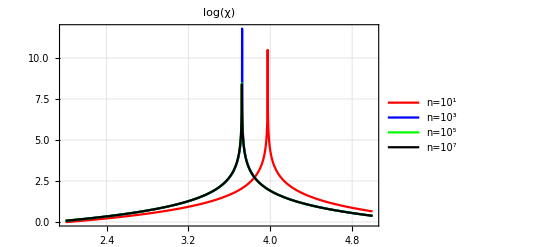

```mathematica
ps1 = Plot[{Log[Abs[xi1]]/.n-> 10/.g-> 1/.r-> 1/(8 √3)},{b,2,5},PlotStyle->Red,PlotRange->All,PlotLegends-> {"n=10^1"},Frame->True,GridLines->Automatic];
ps2 = Plot[{Log[Abs[xi1]]/.n-> 1000/.g-> 1/.r-> 1/(8 √3)},{b,2,5},PlotStyle->Blue,PlotRange->All,PlotLegends-> {"n=10^3"},Frame->True,GridLines->Automatic];
ps3 = Plot[{Log[Abs[xi1]]/.n-> 100000/.g-> 1/.r-> 1/(8 √3)},{b,2,5},PlotStyle->Green,PlotRange->All,PlotLegends-> {"n=10^5"},Frame->True,GridLines->Automatic];
ps4 = Plot[{Log[Abs[xi1]]/.n-> 10000000/.g-> 1/.r-> 1/(8 √3)},{b,2,5},PlotStyle->Black,PlotRange->All,PlotLegends-> {"n=10^7"},Frame->True,GridLines->Automatic];
Show[ps1,ps2,ps3, ps4,PlotLabel->Log[χ],AxesLabel->{β},LabelStyle->Directive[Bold]]
```

Plot susceptibility for different polygons

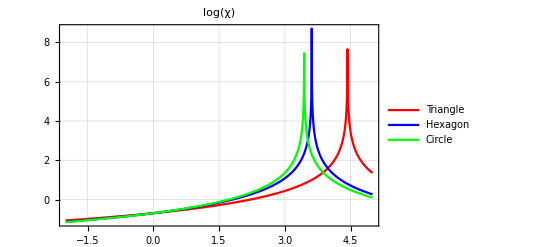

```mathematica
ps1 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 10000000/.g-> 1/.r-> 1/(12 √3)},{b,-2,5},PlotStyle->Red,PlotRange->All,PlotLegends-> {"Triangle"},Frame->True,GridLines->Automatic];
ps2 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 10000000/.g-> 1/.r-> 1/(8 √3)},{b,-2,5},PlotStyle->Blue,PlotRange->All,PlotLegends-> {"Hexagon"},Frame->True,GridLines->Automatic];
ps3 = Plot[{Log[xiCrit22]/.lw-> 4 b g/.n-> 10000000/.g-> 1/.r-> 1/(4Pi)},{b,-2,5},PlotStyle->Green,PlotRange->All,PlotLegends-> {"Circle"},Frame->True,GridLines->Automatic];
Show[ps1,ps2,ps3,PlotLabel->Log[χ],AxesLabel->{β},LabelStyle->Directive[Bold]]
```